```mathematica
1)
```

```mathematica
fa[x_]=2x^3 + 5x^2 + 5
```

5+5 x^2+2 x^3

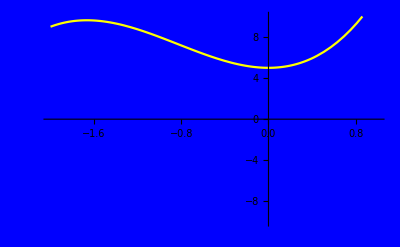

```mathematica
p1 = Plot[fa[x],{x, -2, 1},PlotRange->{-10,10},PlotStyle->Yellow,Background->Blue]
```

```mathematica
Crecimiento Neto
acn=fa[1]-fa[-2]
```

3

```mathematica
Razon de cambio promedio
b-a
arcp = (f[1]-f[-2])/(1+2)
```

cambio de promedio Razon

-a+b

0.

```mathematica
2) 


A)
```

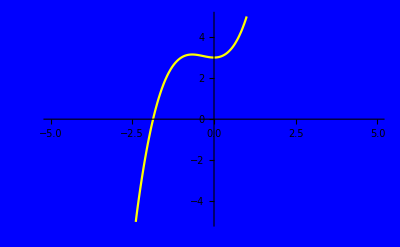

```mathematica
Plot[f[x_]=x^3 + x^2 + 3,{x,-5,5},PlotRange->{-5,5},PlotStyle->Yellow,Background->Blue]
```

```mathematica
Clear[f]
```

```mathematica
f[x_]=x^3 + x^2 +3
```

3+x^2+x^3

```mathematica
f[1/3]
```

85/27

```mathematica
f[-1/3]
```

83/27

```mathematica
m1=f'[-1/3]
```

-1/3

```mathematica
h1=1-m1*(-1/3)
```

8/9

```mathematica
B)
```

```mathematica
msecante=Table[(f[-1/3+h]-f[-1/3])/h,{h,0.05,1/3,0.05}]
```

{-0.330833,-0.323333,-0.310833,-0.293333,-0.270833,-0.243333}

```mathematica
secante=msecante (x+1/3)+f[-1/3]
```

{83/27-0.330833 (1/3+x),83/27-0.323333 (1/3+x),83/27-0.310833 (1/3+x),83/27-0.293333 (1/3+x),83/27-0.270833 (1/3+x),83/27-0.243333 (1/3+x)}

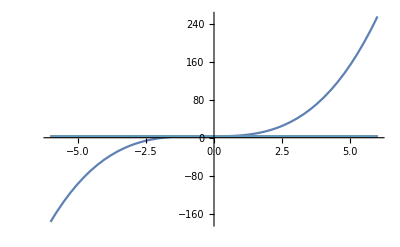

```mathematica
Plot[{f[x],secante,tangente},{x,-6,6}]
```

```mathematica
Animate[Plot[{f[x],((f[-1/3+h]-f[-1/3]) (x+1/3))/h+f[-1/3],tangente},{x,-6,6}],{h,0.1,4,0.05}]
```

```mathematica
3)
```

```mathematica
clear f[x_]
```

clear f[x_]

```mathematica
g[x_]=ⅇ^x
```

ⅇ^x

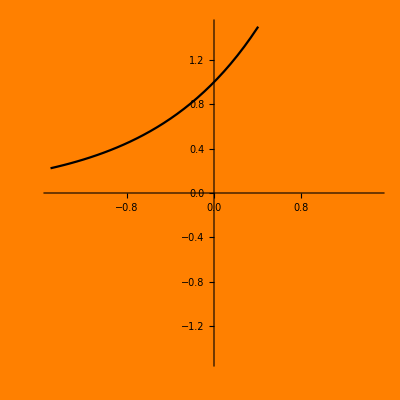

```mathematica
graf=Plot[g[x],{x,-1.5,1.5},PlotStyle->Black,Background->Orange,AxesStyle->White,PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1]
```

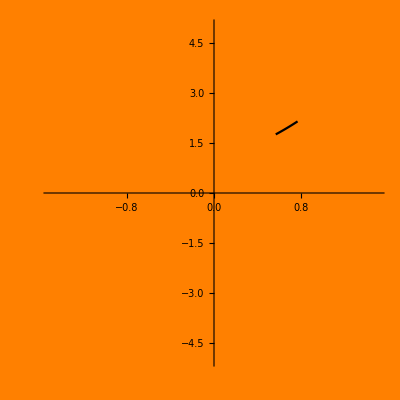

```mathematica
Graf2=Plot[g[x],{x,2/3-(1/10),2/3+(1/10)},PlotStyle->Black,Background->Orange,AxesStyle->White,PlotRange->{{-1.5,1.5},{-5,5}},AspectRatio->1]
```

```mathematica
Rtang=g'[2/3] (x-2/3)+g[2/3]
```

ⅇ^(2/3)+ⅇ^(2/3) (-2/3+x)

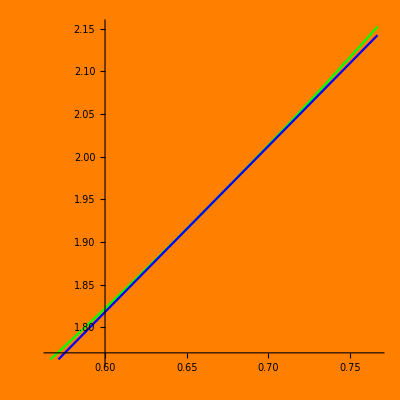

```mathematica
Graf3=Plot[{g[x],Rtang},{x,2/3-(1/10),2/3+(1/10)},PlotStyle->{Green,Blue},Background->Orange,AxesStyle->White,PlotRange->{{2/3-(1/10),2/3+(1/10)},{g[2/3-(1/10)],g[2/3+(1/10)]}},AspectRatio->1]
```

```mathematica
g[0.5]
```

1.64872

```mathematica
dif=g[0.5]+g'[0.5] 0.01
```

1.66521

```mathematica
%%-%
```

-0.0164872

```mathematica
4)
```

```mathematica
ClearAll
```

ClearAll

```mathematica
j[x_]=ⅇ^(x^2)
```

ⅇ^(x^2)

```mathematica
j'[x]
```

2 ⅇ^(x^2) x

```mathematica
Solve[j'[x]==0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

```mathematica
j[-1]
```

ⅇ

```mathematica
j[1]
```

ⅇ

```mathematica
Los intervalos de monotonia estan definidos en el punto en donde la derivada primera se hace 0. Por lo tanto en esta función los intervalos de monotonia son (-∞, 0);(0,+∞)"
```

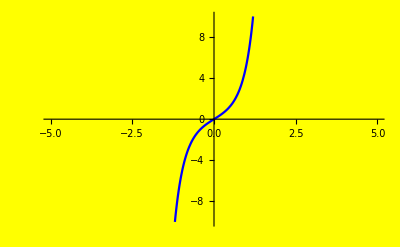

```mathematica
Plot[j'[x],{x,-5,5},PlotRange->{-10,10},PlotStyle->Blue,Background->Yellow]
```

```mathematica
La derivada primera es positiva de (0; +∞) y negativa de (-∞; o)
```

```mathematica
Clear [f]
```

```mathematica
f[x_]=(3x-5)/(2x+4)
```

(-5+3 x)/(4+2 x)

```mathematica
f'[x]//Expand
```

10/(4+2 x)^2-(6 x)/(4+2 x)^2+3/(4+2 x)

```mathematica
Solve[f'[x]==0]
```

{}

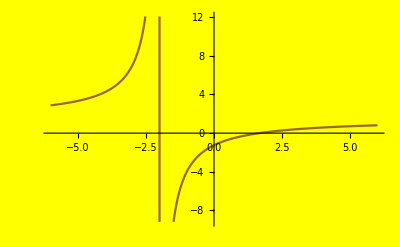

```mathematica
Plot[f[x],{x,-6,6},PlotStyle->Brown,Background->Yellow]
```

```mathematica
Es creciente en todo su dominio
```

```mathematica
5) 


Verificando que:
 Si f(x) esta definida en  D=[a,b] y c,d ∈ D 
Si c es un punto critico de una funcion continua y derivable en unentorno reducido de centro c
Si f(x) si tiene un extremo relativo en x = c  entonces C es un punto critico 

determinio de los dominios
```

```mathematica
Clear[g]
```

```mathematica
g[x_]=x^3/(x+3)
```

x^3/(3+x)

```mathematica
g'[x]
```

-x^3/(3+x)^2+(3 x^2)/(3+x)

```mathematica
Solve[g'[x]==0]
```

{{x→-9/2},{x→0},{x→0}}

```mathematica
g[-9/2]
```

243/4

```mathematica
g[0]
```

0

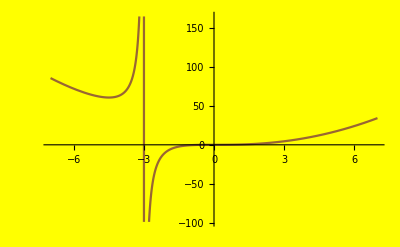

```mathematica
Plot[g[x],{x,-7,7},PlotStyle->Brown,Background->Yellow]
```

```mathematica
intervalos de monotonia:(-∞;-9/2)(-9/2;0)(0;+∞)
```

```mathematica
6) 

el punto P de la curva denominada punto de inflexion en la grafica cambia de concava hacia abajo a concava hacia arriba.
```

```mathematica
Clear[h]
```

```mathematica
h[x_]=Sinh [x]
```

Sinh[x]

```mathematica
h''[x]
```

Sinh[x]

```mathematica
Solve[h[x]==0]
```

{{Sinh[x]→0}}

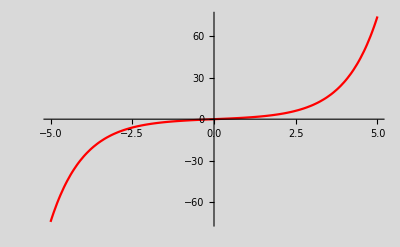

```mathematica
Plot[h[x],{x,-5,5},PlotStyle->Red,Background->LightGray]
```

```mathematica
Intervalos de concavidad:(-∞, 0) (0, +∞) y el punto de inflexion es 0.
una funcion es concava hacia arriba si F.b4(X) es creciente en I
```

```mathematica
7) Propuesta  sección 6.4)
```

```mathematica
Clear[f]
```

```mathematica
f[x_]=1/3 x^3-5 x^2+8x-3
```

-3+8 x-5 x^2+x^3/3

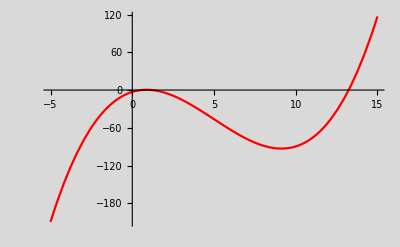

```mathematica
Plot[f[x],{x,-5,15},PlotStyle->Red,Background->LightGray]
```

```mathematica
f'[x]
```

8-10 x+x^2

```mathematica
f''[x]
```

-10+2 x

```mathematica
Solve[f'[x]==0]
```

{{x→5-√17},{x→5+√17}}

```mathematica
Los intervalos de monotonia son (-∞;5-√17)(5-√17;5+√17)(5+√17;+∞)
```

```mathematica
f'[1/2]
f'[1]
f'[10]
```

13/4

-1

8

```mathematica
En el intervalo (-∞;5-√17), la funcion crece
En el intervalo (5-√17;5+√17), la funcion decrece
En el intervalo (5+√17;+∞), la funcion crece
```

```mathematica
Solve[f''[x]==0]
```

{{x→5}}

```mathematica
f''[4]
f''[6]
```

-2

2

```mathematica
En el intervalo (-∞; 5) es concava hacia abajo
En el intervalo (5; +∞) es concava  hacia arriba
```

```mathematica
Limit[f[x],x->-∞]
```

-∞

```mathematica
Limit[f[x],x->+∞]
```

∞

```mathematica
La funcion no posee asintotas
```

```mathematica
N[f[5-√17]]
N[f[5+√17]]
```

0.395197

-93.0619

```mathematica
Hay un máximo local en x=5-√17
Hay un mínimo local en x=5+√17
```

```mathematica
N[Solve[f[x]==0]]
```

{{x→13.2385-8.32667×10^-17 ⅈ},{x→1.19049+1.77636×10^-15 ⅈ},{x→0.571057-1.33227×10^-15 ⅈ}}

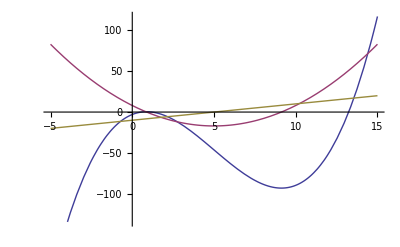

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-5,15},Background->White]
```